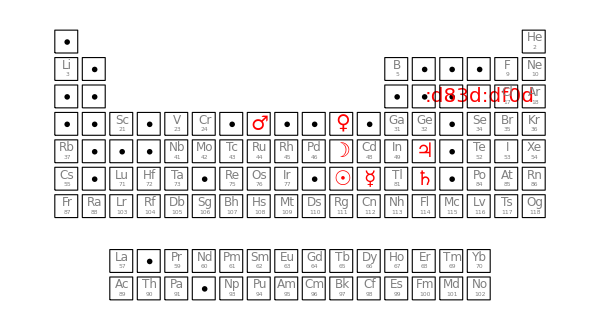

```mathematica
o=Table[Map[ElementData[i,#]&,{"AtomicNumber","Symbol","Period","Group"}],{i,118}];
(*Need to massage the f-block elements,giving them fake groups and periods.Making their periods 9 and 10 with their groups 3 through 16 works nicely*)
o[[57;;70]]=Module[{i=1,rep=Range[3,16],tmp},tmp=Select[o,57≤#[[1]]≤70&]/.{6->9};
tmp/.{Missing["NotApplicable"]:>rep[[i++]]}];
o[[89;;102]]=Module[{i=1,rep=Range[3,16],tmp},tmp=Select[o,89≤#[[1]]≤102&]/.{7->10};
tmp/.{Missing["NotApplicable"]:>rep[[i++]]}];
o=o/.{"Uut"->"Nh","Uup"->"Mc","Uus"->"Ts","Uuo"->"Og"};
alch={{"S"," :d83d:df0d"},{"Hg","☿"},{"Au","☉"},{"Fe","♂"},{"Cu","♀"},{"Pb","♄"},{"Sn","♃"},{"Ag","☽"}};
dalt=Transpose[{daltsyms,dalts}];
ad=Join[alch,dalt];
o=o/.((#[[1]]->#[[2]])&/@alch);
o=o/.((#[[1]]->#[[2]])&/@dalt);
piece=Polygon[{{0,0},{1,0},{1,1},{0,1},{0,0}}];
Clear[box]
box[array_]:=Module[{x,y,m=10},{x,y}=array[[{4,3}]];
{FaceForm[None],EdgeForm[Thin],Rectangle[{m x,m (10-y)},{m (x+1),m (11-y)}]
(*Inset[Style[array[[2]],10,Bold],{m (x+0.5),m(10.7-y)}],Inset[Style[array[[1]],8],{m(x+0.5),m(10.2-y)}]*)}]
makePiece[pt_]:=GeometricTransformation[GeometricTransformation[piece,{pt[[1]],10-pt[[2]]}*{1.2,1.2}],ScalingTransform[{10,10}]];
ptpuzzle=Graphics[{EdgeForm[Thin],FaceForm[None],makePiece/@o[[All,{4,3}]]}];
Clear[letters2]
letters2[array_]:=Module[{x,y,m=10},{x,y}=array[[{4,3}]];
{FaceForm[None],EdgeForm[Thin],(*Rectangle[{m x,m(10-y)},{m(x+1),m(11-y)}]*)Inset[Style[array[[2]],ReleaseHold[If[MemberQ[alch[[All,2]],array[[2]]],Hold[Sequence[20,Red]],Hold[Sequence[12,Gray]]]],FontFamily->"Cambria Math"],{m (x+0.45),m (If[MemberQ[ad[[All,2]],array[[2]]],10.4,10.55]-y)}*{1.2,1.2}],Inset[Style[If[MemberQ[ad[[All,2]],array[[2]]],"",array[[1]]],6,Gray,FontFamily->"Cambria Math"],{m (x+0.45),m (10.2-y)}*{1.2,1.2}]}]
ptpuzzlelt=letters2/@o//Graphics;
Show[ptpuzzlelt,ptpuzzle,ImageSize->600]
```

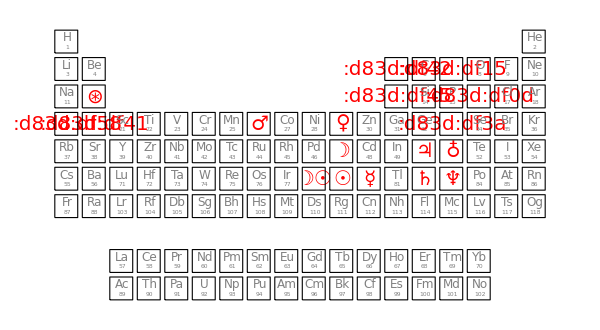

```mathematica
o=Table[Map[ElementData[i,#]&,{"AtomicNumber","Symbol","Period","Group"}],{i,118}];
(*Need to massage the f-block elements,giving them fake groups and periods.Making their periods 9 and 10 with their groups 3 through 16 works nicely*)
o[[57;;70]]=Module[{i=1,rep=Range[3,16],tmp},tmp=Select[o,57≤#[[1]]≤70&]/.{6->9};
tmp/.{Missing["NotApplicable"]:>rep[[i++]]}];
o[[89;;102]]=Module[{i=1,rep=Range[3,16],tmp},tmp=Select[o,89≤#[[1]]≤102&]/.{7->10};
tmp/.{Missing["NotApplicable"]:>rep[[i++]]}];
o=o/.{"Uut"->"Nh","Uup"->"Mc","Uus"->"Ts","Uuo"->"Og"};
alch={{"S"," :d83d:df0d"},{"Hg","☿"},{"Au","☉"},{"Fe","♂"},{"Cu","♀"},{"Pb","♄"},{"Sn","♃"},{"Ag","☽"},{"N"," :d83d:df15"},{"Sb","♁"},{"As"," :d83d:df3a"},{"Bi","♆"},{"B","  :d83d:df42"},{"Mg","⊛"},{"Pt","☽☉ "},{"Ca"," :d83d:df41"},{"Al","  :d83d:df45"},{"K","  :d83d:df58"}};
dalt={};
ad=Join[alch,dalt];
o=o/.((#[[1]]->#[[2]])&/@alch);
o=o/.((#[[1]]->#[[2]])&/@dalt);
piece=Polygon[{{0,0},{1,0},{1,1},{0,1},{0,0}}];
Clear[box]
box[array_]:=Module[{x,y,m=10},{x,y}=array[[{4,3}]];
{FaceForm[None],EdgeForm[Thin],Rectangle[{m x,m (10-y)},{m (x+1),m (11-y)}]
(*Inset[Style[array[[2]],10,Bold],{m (x+0.5),m(10.7-y)}],Inset[Style[array[[1]],8],{m(x+0.5),m(10.2-y)}]*)}]
makePiece[pt_]:=GeometricTransformation[GeometricTransformation[piece,{pt[[1]],10-pt[[2]]}*{1.2,1.2}],ScalingTransform[{10,10}]];
ptpuzzle=Graphics[{EdgeForm[Thin],FaceForm[None],makePiece/@o[[All,{4,3}]]}];
Clear[letters2]
letters2[array_]:=Module[{x,y,m=10},{x,y}=array[[{4,3}]];
{FaceForm[None],EdgeForm[Thin],(*Rectangle[{m x,m(10-y)},{m(x+1),m(11-y)}]*)Inset[Style[array[[2]],ReleaseHold[If[MemberQ[alch[[All,2]],array[[2]]],Hold[Sequence[20,Red]],Hold[Sequence[12,Gray]]]],FontFamily->"Cambria Math"],{m (x+0.45),m (If[MemberQ[ad[[All,2]],array[[2]]],10.4,10.55]-y)}*{1.2,1.2}],Inset[Style[If[MemberQ[ad[[All,2]],array[[2]]],"",array[[1]]],6,Gray,FontFamily->"Cambria Math"],{m (x+0.45),m (10.2-y)}*{1.2,1.2}]}]
ptpuzzlelt=letters2/@o//Graphics;
Show[ptpuzzlelt,ptpuzzle,ImageSize->600]
```

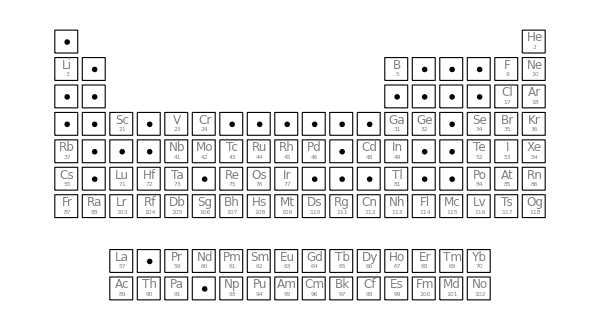

```mathematica
o=Table[Map[ElementData[i,#]&,{"AtomicNumber","Symbol","Period","Group"}],{i,118}];
(*Need to massage the f-block elements,giving them fake groups and periods.Making their periods 9 and 10 with their groups 3 through 16 works nicely*)
o[[57;;70]]=Module[{i=1,rep=Range[3,16],tmp},tmp=Select[o,57≤#[[1]]≤70&]/.{6->9};
tmp/.{Missing["NotApplicable"]:>rep[[i++]]}];
o[[89;;102]]=Module[{i=1,rep=Range[3,16],tmp},tmp=Select[o,89≤#[[1]]≤102&]/.{7->10};
tmp/.{Missing["NotApplicable"]:>rep[[i++]]}];
o=o/.{"Uut"->"Nh","Uup"->"Mc","Uus"->"Ts","Uuo"->"Og"};
alch={{"S"," :d83d:df0d"},{"Hg","☿"},{"Au","☉"},{"Fe","♂"},{"Cu","♀"},{"Pb","♄"},{"Sn","♃"},{"Ag","☽"}};
dalt=Transpose[{daltsyms,dalts}];
ad=Join[alch,dalt];
o=o/.((#[[1]]->#[[2]])&/@dalt);
o=o/.((#[[1]]->#[[2]])&/@alch);
piece=Polygon[{{0,0},{1,0},{1,1},{0,1},{0,0}}];
Clear[box]
box[array_]:=Module[{x,y,m=10},{x,y}=array[[{4,3}]];
{FaceForm[None],EdgeForm[Thin],Rectangle[{m x,m (10-y)},{m (x+1),m (11-y)}]
(*Inset[Style[array[[2]],10,Bold],{m (x+0.5),m(10.7-y)}],Inset[Style[array[[1]],8],{m(x+0.5),m(10.2-y)}]*)}]
makePiece[pt_]:=GeometricTransformation[GeometricTransformation[piece,{pt[[1]],10-pt[[2]]}*{1.2,1.2}],ScalingTransform[{10,10}]];
ptpuzzle=Graphics[{EdgeForm[Thin],FaceForm[None],makePiece/@o[[All,{4,3}]]}];
Clear[letters2]
letters2[array_]:=Module[{x,y,m=10},{x,y}=array[[{4,3}]];
{FaceForm[None],EdgeForm[Thin],(*Rectangle[{m x,m(10-y)},{m(x+1),m(11-y)}]*)Inset[Style[array[[2]],ReleaseHold[If[MemberQ[alch[[All,2]],array[[2]]],Hold[Sequence[20,Red]],Hold[Sequence[12,Gray]]]],FontFamily->"Cambria Math"],{m (x+0.45),m (If[MemberQ[ad[[All,2]],array[[2]]],10.4,10.55]-y)}*{1.2,1.2}],Inset[Style[If[MemberQ[ad[[All,2]],array[[2]]],"",array[[1]]],6,Gray,FontFamily->"Cambria Math"],{m (x+0.45),m (10.2-y)}*{1.2,1.2}]}]
ptpuzzlelt=letters2/@o//Graphics;
Show[ptpuzzlelt,ptpuzzle,ImageSize->600]
```